# 生日问题

## OG

```mathematica
Birthday[x_]:=1-(365!)/(365^x×(365-x)!)
```

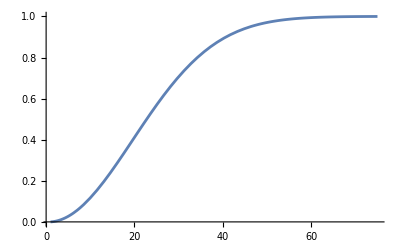

```mathematica
plot1=Plot[Birthday[x],{x,1,75}]
```

## 给定生日概率分布

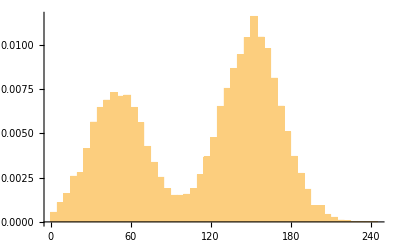

```mathematica
pdf[x_]:=0.4*Exp[-(x-50)^2/1000]+0.6*Exp[-(x-150)^2/1000]
discretePDF=Table[{x,pdf[x]},{x,1,365}];
normalizedPDF=discretePDF[[All,2]]/Total[discretePDF[[All,2]]];
samples=RandomChoice[normalizedPDF->Range[1,365],10000];
Histogram[samples,50,"PDF",ChartLegends->"Sampling from Custom Distribution"]
```

## 自定义生日概率分布

```mathematica
(*假设每个月份的概率*)monthProbs={0.07,0.08,0.08,0.08,0.1,0.15,0.08,0.08,0.09,0.07,0.06,0.06};
monthProbs={0.1,0.1,0.1,0.05,0.2,0.05,0.1,0.1,0.1,0.05,0.2,0.05};
(*对应每个月份的天数*)
daysInMonth={31,28,31,30,31,30,31,31,30,31,30,31};

(*逐步生成每一天的概率，避免一次性构建大数组*)
dayProbs=Flatten[Table[ConstantArray[monthProbs[[i]],daysInMonth[[i]]],{i,Length[monthProbs]}]];

(*归一化概率分布*)
dayProbs=dayProbs/Total[dayProbs];

(*输出以验证 dayProbs 结构的正确性*)
dayProbs[[1;;10]] (*查看前10个生成的概率*)
```

{0.00273973,0.00273973,0.00273973,0.00273973,0.00273973,0.00273973,0.00273973,0.00273973,0.00273973,0.00273973}

## 蒙特卡洛模拟

### 单次蒙特卡洛模拟

```mathematica
(*您的自定义概率分布*)
pList=Normalize[RandomReal[1,365],Total];  
pList = dayProbs;
(*模拟函数*)
simulateTrial[x_]:=Module[{birthdays},birthdays=RandomChoice[pList->Range[365],x];
Length[birthdays]!=Length[DeleteDuplicates[birthdays]]]

simulateBirthdayParadox[x_,N_]:=Module[{trials},trials=Table[simulateTrial[x],{N}];
N[Mean[Boole[trials]]]]

(*进行模拟*)
probabilityEstimate=simulateBirthdayParadox[23,100000]//N

(*输出结果*)
Print["在50个人的情况下，至少有两个人生日相同的概率估计为：",probabilityEstimate]
```

100000.[0.58699]

在50个人的情况下，至少有两个人生日相同的概率估计为：100000.[0.58699]

### 模拟生日-人数函数

```mathematica
(*模拟函数*)simulateTrial[x_]:=Module[{birthdays},birthdays=RandomChoice[pList->Range[365],x];
Length[birthdays]!=Length[DeleteDuplicates[birthdays]]]

simulateBirthdayParadox[x_,N_]:=Module[{trials,successes},trials=Table[simulateTrial[x],{N}];
successes=Count[trials,True];
successes/N  (*这里不使用N[]，直接进行数值除法*)]

(*设置模拟次数*)
numSimulations=100000;

(*计算人数从1到75的概率*)
probabilities=Table[N[simulateBirthdayParadox[x,numSimulations]],{x,1,75}];
```

## Visualization

```mathematica
(*绘制概率随人数增加的曲线*)
plot2=ListLinePlot[probabilities,PlotRange->{0,1},AxesLabel->{"人数","概率"},PlotLabel->"至少两人生日相同的概率随人数的变化",PlotMarkers->Automatic]
```

```mathematica
Show[plot1,plot2]
```

monthProbs={0.1,0.1,0.1,0.05,0.2,0.05,0.1,0.1,0.1,0.1,0.1,0.1};

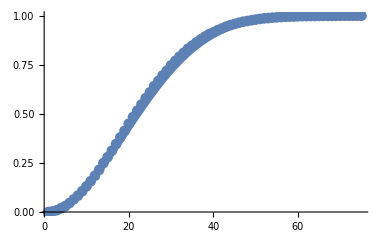

monthProbs = {0.1, 0.1, 0.1, 0.05, 0.2, 0.05, 0.1, 0.1, 0.1, 0.05, 0.2, 0.05};